```mathematica
Needs["PlotLegends`"]
SetDirectory[FileNameJoin[{NotebookDirectory[]}]]

Parameters = Import["../Parameters"]

n=Parameters[[4,2]]
L=IntegerPart[Parameters[[2,2]]]
m=Parameters[[3,2]]

κ=IntegerPart[Parameters[[6,2]]]
ηb=Parameters[[5,2]]

IntactPF=Import["../Intact/PartitionFunction_0_0.out","Table"];
IntactFE=Import["../Intact/FreeEnergy_0_0.out","Table"];
IntactdFE=Import["../Intact/dFreeEnergy_0_0.out","Table"];

BubblePF31=Import["PartitionFunction_3_1.out","Table"];
BubbleFE31=Import["FreeEnergy_3_1.out","Table"];
BubbledFE31=Import["dFreeEnergy_3_1.out","Table"];

BubblePF21=Import["PartitionFunction_2_1.out","Table"];
BubbleFE21=Import["FreeEnergy_2_1.out","Table"];
BubbledFE21=Import["dFreeEnergy_2_1.out","Table"];

BubblePF22=Import["PartitionFunction_2_2.out","Table"];
BubbleFE22=Import["FreeEnergy_2_2.out","Table"];
BubbledFE22=Import["dFreeEnergy_2_2.out","Table"];

BubblePF13=Import["PartitionFunction_1_3.out","Table"];
BubbleFE13=Import["FreeEnergy_1_3.out","Table"];
BubbledFE13=Import["dFreeEnergy_1_3.out","Table"];
```

/homes/ht/Desktop/workspace/dna_results/Nucleation_0p5/results/Bubble

{{},{L:,20.},{m:,40},{N:,5},{eta_b:,0.5},{kappa_sigma_r:,1.},{Delta:,0.2469},{},{Extension Minimum:,0},{Extension Maximum:,25},{TOLERANCE:,0.}}

5

20

40

1

0.5

## Numerical Results

### Bubble - Partition Function and Free Energy

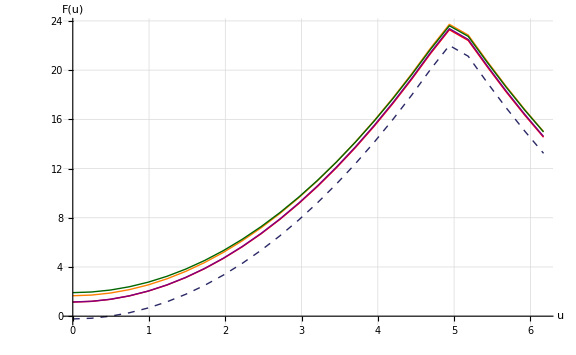

```mathematica
fsTitle=24;
fsAxesLabel=18;
fs2=16;

pIntact=ListLinePlot[IntactFE,PlotStyle->{Thick,Dashed,Darker[ColorData[1,1]]}];
pBubbleFE31=ListLinePlot[BubbleFE31,PlotStyle->{Thick,Red}];
pBubbleFE21=ListLinePlot[BubbleFE21,PlotStyle->{Thick,Purple}];
pBubbleFE22=ListLinePlot[BubbleFE22,PlotStyle->{Thick,Orange}];pBubbleFE13=ListLinePlot[BubbleFE13,PlotStyle->{Thick,Darker[Green,0.6]}];

legend={{Graphics[{Thick,Dashed,Darker[ColorData[1,1]],Line[{{0,0},{2,0}}]}],Style["Intact",FontSize->fs2]},{Graphics[{Thick,Red,Line[{{0,0},{2,0}}]}],Style["Bubble (3,1)",FontSize->fs2]},
{Graphics[{Thick,Purple,Line[{{0,0},{2,0}}]}],Style["Bubble (2,1)",FontSize->fs2]},
{Graphics[{Thick,Orange,Line[{{0,0},{2,0}}]}],Style["Bubble (2,2)",FontSize->fs2]},
{Graphics[{Thick,Darker[Green,0.6],Line[{{0,0},{2,0}}]}],Style["Bubble (1,3)",FontSize->fs2]}
};

plot=ShowLegend[
Show[{pIntact,pBubbleFE31,pBubbleFE21,pBubbleFE22,pBubbleFE13},ImageSize->Large,GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],AxesOrigin->{0,0},PlotRange->All,AxesLabel->{Style["u",FontSize->fsAxesLabel],Style["F(u)",FontSize->fsAxesLabel]},LabelStyle->{"Times",FontSize->fs2}],
{legend,LegendShadow->None,LegendBorder->None,LegendBackground->Opacity[0],ShadowBackground->Opacity[0],LegendSize->{0.5,0.5},LegendPosition->{-0.8,0.05}}
]
```

```mathematica
Export["Bubble_N"<>ToString[n]<>"_L"<>ToString[L]<>"_m"<>ToString[m]<>"_kappa"<>ToString[κ]<>"_etab"<>ToString[ηb]<>".pdf",plot]
```

Bubble_N5_L20_m40_kappa1_etab0.5.pdf